```mathematica
Clear["Global`*"]
```

```mathematica
NotebookDirectory[]
```

D:\Dropbox\ExtractIPD\process\

```mathematica
AR=Import[NotebookDirectory[]<>"AR.csv","CSV"];
```

```mathematica
AR//TableForm
```

interval | trisk | lower | upper | nrisk | TE | Slide | Arm | Subpop
1 | 0 |  |  | 12 | 12 | A | pembrolizumab | ITT
2 | 1 |  |  | 7 | 12 | A | pembrolizumab | ITT
3 | 2 |  |  | 5 | 12 | A | pembrolizumab | ITT
4 | 3 |  |  | 0 | 12 | A | pembrolizumab | ITT

```mathematica
KM=Import[NotebookDirectory[]<>"F_OS_CPS_1_pembrolizumab.csv","CSV"]⟦All,{1,2}⟧;
```

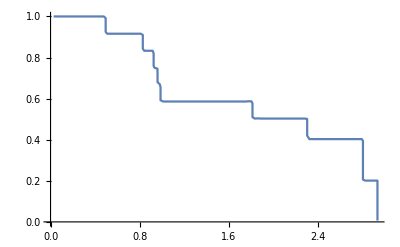

```mathematica
ListPlot[KM⟦2;;-1;;20⟧,Joined->True]
```

```mathematica
InitialPopulation=AR⟦2,5⟧
```

12

```mathematica
FinalSurvivalFraction=Min[Select[Map[ToExpression,KM⟦2;;,2⟧],#>-1&]]

FinalSurvivalFraction=0
```

0.00648

0

```mathematica
TotalEvents=Floor[InitialPopulation*(1-FinalSurvivalFraction)]
```

12

```mathematica
ColumnHeight=Max[Select[AR⟦All,1⟧,NumberQ[ToExpression[#]]&]]+1
```

5

```mathematica
TotalEventsColumn=Prepend[Table[TotalEvents,{ColumnHeight-1}],"TE"]
```

{TE,12,12,12,12}

```mathematica
ARtableFixed={AR⟦All,1⟧,AR⟦All,2⟧,AR⟦All,3⟧,AR⟦All,4⟧,AR⟦All,5⟧,TotalEventsColumn,AR⟦All,7⟧,AR⟦All,8⟧,AR⟦All,9⟧}ᵀ;

ARtableFixed//TableForm
```

interval | trisk | lower | upper | nrisk | TE | Slide | Arm | Subpop
1 | 0 |  |  | 12 | 12 | A | pembrolizumab | ITT
2 | 1 |  |  | 7 | 12 | A | pembrolizumab | ITT
3 | 2 |  |  | 5 | 12 | A | pembrolizumab | ITT
4 | 3 |  |  | 0 | 12 | A | pembrolizumab | ITT

```mathematica
Export[NotebookDirectory[]<>"AR.csv",ARtableFixed,"CSV"]
```

D:\Dropbox\ExtractIPD\process\AR.csv

```mathematica
(*
Export[NotebookDirectory[]<>ToString[TotalEvents]<>".txt",TotalEvents,"Text"]
*)
```

D:\Dropbox\ExtractIPD\process\426.txt